```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={a>0,n≥i,Element[n,Integers],Element[i,Integers],Element[a,Reals],ϵ>0&&Element[ϵ,Reals]}
```

{a>0,n≥i,n∈ℤ,i∈ℤ,a∈ℝ,ϵ>0&&ϵ∈ℝ}

```mathematica
(*Real-space bounds (In bohr radii)*)
x0=-10;xf=10;
(*Number of discretization points*)
n=10;
(*Resulting mesh spacing*)
δ=(xf-x0)/n;

(*Defining boundary conditions*)
bc1=0;bc2=0;

(*ℏ, k, and m are measured in atomic units and are therefore 1*)
ℏ=1;m=1;
k=1;ω=√(k/m);
```

```mathematica
x[i_]=x0+i δ;
V[i_]=1/2 m ω^2 x[i]^2;

(*ϵ ψ[x]==-ℏ^2/(2 m) ψ''[x]+V[x] ψ[x] -> H[x]==(-ℏ^2/(2 m) D[#,{x,2}]+V[x] # )&*)
H[i_]:=-ℏ^2/(2 m) 1/δ^2(Indexed[ψ,i+1]-2 Indexed[ψ,i]+Indexed[ψ,i-1])+V[i] Indexed[ψ,i]==0
```

```mathematica
functable=Table[H[i],{i,2,n}];
functable=Prepend[functable, Indexed[ψ,1]==bc1];
functable=Append[functable, Indexed[ψ,n+1]==bc2];
vartable=Table[Indexed[ψ,i],{i,1,n+1}];
```

```mathematica
arrays=CoefficientArrays[functable,vartable];
A=arrays[[2]]//N;
b=arrays[[1]];
```

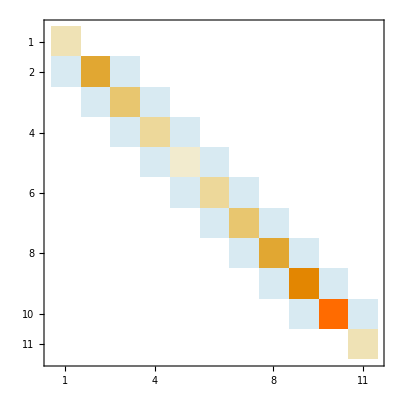

```mathematica
MatrixPlot[A]
```

```mathematica
norm=Norm[A,"Frobenius"];
transformedA = norm*IdentityMatrix[n+1]-A;
```

```mathematica
shiftedVals=Eigenvalues[transformedA,5,Method->{"Direct"}];
Vals=-shiftedVals+norm
```

{0.5,1.,1.,1.5,2.5}

```mathematica
(*x=ConstantArray[1,n+1]/(n+1);
eigV=FixedPoint[((transformedA.#)/Norm[transformedA.#])&,x,100000];
-(eigV.transformedA.eigV)/(eigV.eigV)+norm*)
```